Data Stock

369

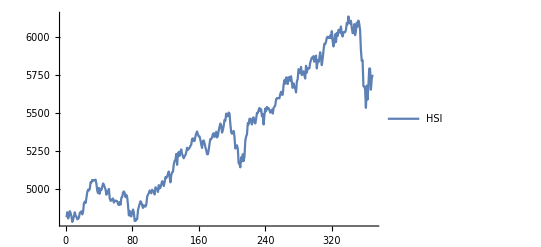

```mathematica
Stock Data

stockData =  FinancialData["^FTSE",{DateObject[{2005,1,1}],DateObject[{2006,6,1}]}];
stockPrices =stockData[[All, 2]];
allRealPrices = stockPrices[[2;;-1]];
allBeforeRealPrices = stockPrices[[1;;-2]];
priceChanges = allRealPrices / allBeforeRealPrices;
Length[stockPrices]
plot = ListLinePlot[{stockPrices},PlotLegends->{"HSI"}]
```

```mathematica
Predictors

sampleSize=300;
windowSize=4;
methods = {"NearestNeighbors", "NeuralNetwork", "RandomForest", "LinearRegression"};
(*methods = {"NeuralNetwork"};*)

iterations = sampleSize;
SetSharedVariable[iterations];
predictedPrices = Monitor[ParallelTable[
iterations++;
patterns = Table[priceChanges[[j;;j+windowSize-1]]->priceChanges[[j+windowSize]], {j, i-sampleSize+1,i-windowSize}];
trainingPatterns = patterns[[1;;-2]];
testPatterns = patterns[[-1]];
predictors = Predict[trainingPatterns, Method ->#, PerformanceGoal->"Quality"]&/@  methods;
(*If [i == sampleSize, Print[PredictorInformation[#]] & /@ predictors];*)
#[Keys[testPatterns]]  * allBeforeRealPrices[[i]] & /@  predictors
, {i,sampleSize,Length[priceChanges]}],ProgressIndicator[iterations, {sampleSize,Length[priceChanges]}]];
realPrices = allRealPrices[[-Length[predictedPrices];;-1]];
beforeRealPrices = allRealPrices[[-Length[predictedPrices]-1;;-2]];
predictedPricesAllMethods = predictedPrices;
AppendTo[methods,"Naive"];
predictedPricesAllMethods = Append[predictedPricesAllMethodsᵀ,beforeRealPrices]ᵀ;
```

Predictors

```mathematica
Predictor results

measures = {};
For[i=1, i ≤Length[methods], i++,
predictedPrices = predictedPricesAllMethods[[All,i]];

mae = Total[Abs[ predictedPrices-realPrices]] / Length[realPrices];
mape = Total[Abs[ predictedPrices/realPrices-1]] / Length[realPrices]*100;
mapeNaive = Total[Abs[  predictedPrices/ predictedPricesAllMethods[[All,5]]-1]] / Length[realPrices]*100;

movementAccuracy = Total[(Sign[predictedPrices-beforeRealPrices] * Sign[realPrices-beforeRealPrices]+1)/2] / Length[realPrices];

money = 1;
For [t = 2, t ≤Length[predictedPrices], t++,
If [predictedPrices[[t]] ≥realPrices[[t-1]], 
money *= realPrices[[t]] / realPrices[[t-1]];
]
];
moneyNoFees = money;

money = 1;
hasInvested = True;
For [t = 2, t ≤Length[predictedPrices], t++,
transactionFee = money * 0.14 / 100;

If [hasInvested,
If [predictedPrices[[t]] + transactionFee <realPrices[[t-1]],  
money -= transactionFee;
hasInvested=False;
,
money *= realPrices[[t]] / realPrices[[t-1]];
]
,
If [predictedPrices[[t]] - transactionFee ≥realPrices[[t-1]],  
money = (money-transactionFee)*realPrices[[t]] / realPrices[[t-1]];
hasInvested=True;
]
];

]
AppendTo[measures,{mae, mape, mapeNaive, moneyNoFees, money, N[movementAccuracy]}];
]
table = TableForm[measures,TableHeadings->{methods, {"MAE", "MAPE", "MAPE naive","Investment profit no fees", "Investment profit", "Movement accuracy"}}]

(*Manipulate[ListLinePlot[fs],{fs,funcs,ControlType->TogglerBar}]*)
plotMethods = Append[methods, "Real"];
funcs=Append[predictedPricesAllMethodsᵀ, realPrices];
Manipulate[ListLinePlot[funcs[[Position[plotMethods, #][[1,1]] & /@ x]], PlotLegends->x, ImageSize->Large], {{x, {"Real"}, "zebra"},plotMethods, ControlType->TogglerBar}]

(*ListLinePlot[{realPrices, predictedPricesAllMethods[[All,1]], predictedPricesAllMethods[[All,2]], predictedPricesAllMethods[[All,3]], predictedPricesAllMethods[[All,4]]},PlotLegends->{"Real prices", "Predicted Prices"}]*)
```

Predictor results

| MAE | MAPE | MAPE naive | Investment profit no fees | Investment profit | Movement accuracy
NearestNeighbors | 42.143 | 0.719098 | 0.110339 | 1.0073 | 0.959103 | 0.565217
NeuralNetwork | 41.9521 | 0.715593 | 0.138992 | 0.970546 | 0.938455 | 0.521739
RandomForest | 41.995 | 0.716594 | 0.158846 | 0.972907 | 0.939421 | 0.550725
LinearRegression | 42.6456 | 0.727206 | 0.0727554 | 0.978522 | 0.975785 | 0.507246
Naive | 42.0348 | 0.716587 | 1.12631×10^-15 | 0.978522 | 0.978522 | 0.5

```mathematica
Classifiers

sampleSize = 30;
windowSize =1;
methods = {"NaiveBayes", "LogisticRegression", "NearestNeighbors", "NeuralNetwork", "SupportVectorMachine","RandomForest"};
methods = {"NeuralNetwork"};
priceChanges = allRealPrices;
predictedPrices = ParallelTable[
patterns = Table[priceChanges[[j;;j+windowSize-1]]->Sign[priceChanges[[j+windowSize]]-priceChanges[[j+windowSize-1]]], {j, i-sampleSize+1,i-windowSize}];
trainingPatterns = patterns[[1;;-2]];
testPatterns = patterns[[-1]];
predictors = Classify[trainingPatterns, Method ->#, PerformanceGoal->"TrainingSpeed"]&/@  methods;
(*If [i == sampleSize, Print[ClassifierInformation[#]] & /@ predictors];*)
#[Keys[testPatterns]] & /@  predictors
, {i,sampleSize,Length[priceChanges]}]
realPrices = allRealPrices[[-Length[predictedPrices];;-1]];
beforeRealPrices = allRealPrices[[-Length[predictedPrices]-1;;-2]];
predictedPricesAllMethods = predictedPrices;

AppendTo[methods,"Naive"]
predictedPricesAllMethods = Append[predictedPricesAllMethodsᵀ,beforeRealPrices]ᵀ;
```

```mathematica
Classifiers results

measures = {};
For[i=1, i ≤Length[methods], i++,
predictedPrices = predictedPricesAllMethods[[All,i]];
movementAccuracy = Total[(predictedPrices * Sign[realPrices-beforeRealPrices]+1)/2] / Length[realPrices];
money = 1;
For [t = 2, t ≤Length[predictedPrices], t++,
If [predictedPrices[[t]] > 0,
money *= realPrices[[t]] / realPrices[[t-1]];
]
];
AppendTo[measures,{N[(money-1),3]*100, N[movementAccuracy,3]*100}]
]


table = TableForm[measures,TableHeadings->{methods, {"Investment profit", "Movement accuracy"}}]

ListPlot
```

| Investment profit | Movement accuracy
NeuralNetwork | -2.03112 | 44.9
Naive | -0.610889 | -7064.94

ListPlot